```mathematica
SetOptions[$FrontEndSession,EvaluationCompletionAction->"ShowTiming"];
CurrentValue[EvaluationNotebook[],DefaultNaturalLanguage]="English";
```

# PS3 - Dynamical Systems // Physics Institute UdeA // 2017-1 Juan Esteban Aristizábal Zuluaga Last update: Apr 18th 2017

## P.1

4.3.3	 θ̇=μ sinθ-sin 2θ  without loss of generality the domain will be taken over -π<θ≤π.08.08.08

```mathematica
f1[θ_,μ_]:=μ Sin[θ]-Sin[2 θ]
```

Fixed points:

```mathematica
{θf11,θf12,θf13,θf14}=θ/.Simplify[Solve[f1[θ,μ]==0,θ]]/.C[1]->0
```

{0,π,ArcTan[μ,-√(4-μ^2)],ArcTan[μ,√(4-μ^2)]}

```mathematica
{{μcf11,θcf11},{μcf12,θcf12}}={μ,θ}/.Solve[{f1[θ,μ]==0,D[f1[θ,μ],θ]==0},{θ,μ}]/.C[1]->0
```

{{-2,π},{2,0}}

The critic values are μ_c=±2 , μ_c=0

Linear stability analysis:

```mathematica
{staf11,staf12,staf13,staf14}=D[f1[θ,μ],θ]/.θ->{θf11,θf12,θf13,θf14}
```

{-2+μ,-2-μ,μ^2/2-2 Cos[2 ArcTan[μ,-√(4-μ^2)]],μ^2/2-2 Cos[2 ArcTan[μ,√(4-μ^2)]]}

In the bifurcation diagram: 
	The branch θ^*=0 is stable for μ<2  and unstable for μ>2
	The branch θ^*=±π (they are the same one –flows on the circle) is stable for μ>-2  and unstable for  μ<-2
	The branches θ^*=ArcTan[μ,±√(4-μ^2)]  are always unstable.

```mathematica
Reduce[μ^2/2-2 Cos[2 ArcTan[-√((4/μ^2)-1)]]>0,μ,Reals]
Reduce[μ^2/2-2 Cos[2 ArcTan[√((4/μ^2)-1)]]>0,μ,Reals]
```

-2<μ<0||0<μ<2

-2<μ<0||0<μ<2

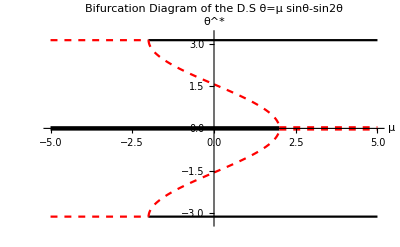

```mathematica
a11=
Plot[
θf11,{μ,-5,2},
PlotStyle->{Black,Thickness[0.008]}
];

a12=
Plot[
θf11,{μ,2,5},
PlotStyle->{Red,Dashed,Thickness[0.008]}
];

a13=
Plot[
{θf12,-π},{μ,-5,-2},
PlotStyle->{{Red,Dashed},{Red,Dashed}}
];

a14=
Plot[
{θf12,-π},{μ,-2,5},
PlotStyle->{{Black},{Black}}
];

a15=
Plot[
{θf13,θf14},{μ,-2,2},
PlotStyle->{{Red,Dashed},{Red,Dashed}}
];
Show[a11,a12,a13,a14,a15,PlotRange->{{-5,5},{-π-0.2,π+0.2}},AxesLabel->{"μ","θ^*"},PlotLabel->"Bifurcation Diagram of the D.S\nθ̇=μ sinθ-sin2θ"]
```

The bifurcations in μ=±2 are sub-critical pitchforks (the bifurcation diagram could be extended periodically over the θ^* axis if the domain is selected otherwise)

4.3.3	 θ̇=μ +sinθ+cos 2θ  without loss of generality the domain will be taken over -π<θ≤π.08.08.08

```mathematica
f2[θ_,μ_]:=μ +Sin[θ]+Cos [2 θ]
```

Fixed points:

```mathematica
{θf21,θf22,θf23,θf24}=θ/.(Simplify[Solve[f2[θ,μ]==0,θ]]/.C[1]->0)
```

{ArcTan[-√2 √(3-4 μ-√(9+8 μ)),1+√(9+8 μ)],ArcTan[√2 √(3-4 μ-√(9+8 μ)),1+√(9+8 μ)],ArcTan[-√2 √(3-4 μ+√(9+8 μ)),1-√(9+8 μ)],ArcTan[√2 √(3-4 μ+√(9+8 μ)),1-√(9+8 μ)]}

Bifurcation points:

```mathematica
{{μcf21,θcf21},{μcf22,θcf22},{μcf23,θcf23},{μcf24,θcf24}}={μ,θ}/.Solve[{f2[θ,μ]==0,D[f2[θ,μ],θ]==0},{θ,μ}]/.C[1]->0
```

{{-9/8,π-ArcTan[1/(√15)]},{-9/8,ArcTan[1/(√15)]},{0,π/2},{2,-π/2}}

The critic values are μ_c=-9/8 , μ_c=0 , μ_c=2
We will analyze graphically the stability of the fixed points. Taking μ=-1, the fixed points are:

```mathematica
{θf21,θf22,θf23,θf24}/.μ->-1
```

{(5 π)/6,π/6,π,0}

And the plot θ̇  vs. θ:

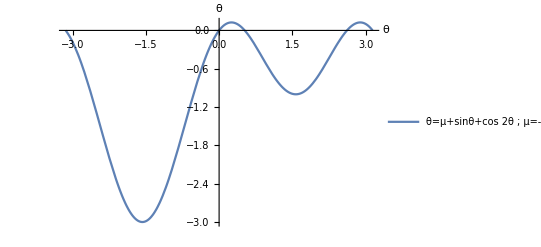

```mathematica
Plot[
f2[θ,-1],{θ,-π,π},
AxesLabel->{"θ","θ̇"},
PlotLegends->{"θ̇=μ+sinθ+cos 2θ  ;  μ=-1"}
]
```

So, 
	The branch related to the fixed point θ^*=5/6 π   (θ^*=ArcTan[-√2 √(3-4 μ-√(9+8 μ)),1+√(9+8 μ)])  must be unstable (positive slope).
	The branch related to the fixed point θ^*=1/6 π   (θ^*=ArcTan[√2 √(3-4 μ-√(9+8 μ)),1+√(9+8 μ)]) must be stable (positive slope).
	The branch related to the fixed point θ^*=π   (θ^*=ArcTan[-√2 √(3-4 μ+√(9+8 μ)),1-√(9+8 μ)]) must be stable (positive slope).
	The branch related to the fixed point θ^*=0   (θ^*=ArcTan[√2 √(3-4 μ+√(9+8 μ)),1-√(9+8 μ)]) must be unstable (positive slope).
	
Graphically:

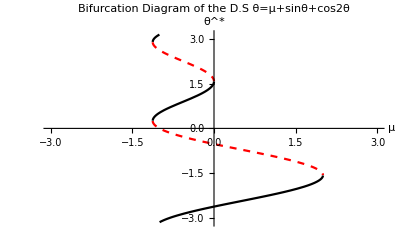

```mathematica
a21=
Plot[
{θf21,θf24},{μ,-3,3},
PlotStyle->{{Red,Dashed},{Red,Dashed}}
];
a22=
Plot[
{θf22,θf23},{μ,-3,3},
PlotStyle->{{Black},{Black}}
];
Show[
a21,a22,PlotRange->{{-3,3},{-π,π}},
AxesLabel->{"μ","θ^*"},
PlotLabel->"Bifurcation Diagram of the D.S\nθ̇=μ+sinθ+cos2θ"
]
```

The bifurcations that occur at μ=-9/8  ,μ=0  and  μ=2 are all saddle-nodes.

## P. II

4.5.1.

Our dynamical system is Θ̇=Ω   ;  θ̇=ω+A f(Θ-θ)    with  f(ϕ)=Piecewise[{{ϕ,, -π/2≤ϕ≤π/2}, {π-ϕ,, π/2<ϕ≤(3π)/2}}]
Introducing the new variable    ϕ=Θ-θ     →    ϕ̇=Θ̇-θ̇=Ω-ω-A f(ϕ)  and setting τ=A t , μ=(Ω-ω)/A we get our dimensionless system:

ⅆϕ/ⅆτ=μ-f(ϕ)

a) Without loss of generality the domain will be taken over -π<ϕ≤π. Thus, we reset the function as

f(ϕ)=Piecewise[{{, }}]-ϕ+π, | -π<ϕ≤(-3π)/2
ϕ, | (-3π)/2<ϕ≤(3π)/2
-ϕ-π, | (3π)/2<ϕ≤π

```mathematica
f3[ϕ_]:=Piecewise[{{ϕ,0≤ϕ≤π/2},{π-ϕ,π/2<ϕ≤(3π)/2},{ϕ-2π,(3π)/2<ϕ≤2π}}]
f31[ϕ_]:=Piecewise[{{f3[Mod[ϕ,2π]],ϕ≥0},{-f3[Mod[-ϕ,2π]],ϕ<0}}]
```

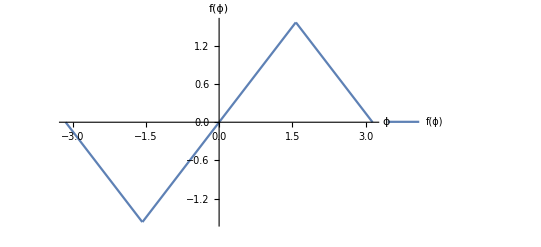

```mathematica
Plot[
f31[ϕ],{ϕ,-π,π},
PlotLegends->{{"f(ϕ)"}},
AxesLabel->{"ϕ","f(ϕ)"}
]
```

b) The range of entrainment is determined by that in which the dynamical system has  at least one fixed point. Thus, it is given by:

-π/2 ≤ μ ≤π/2
                        -π/2 ≤ (Ω-ω)/A ≤ π/2
Thus,

                 ω-A π/2 ≤ Ω ≤ ω+A π/2

c) The phase difference ϕ^* when the firefly is phase-locked to the stimulus is given by:

0=μ-f(ϕ^*)
f(ϕ^*)=μ

Therefore, as the firefly is phase-locked to the stimulus, the only stable fixed point (the phase difference) is given by

ϕ^*=μ

ϕ^*=(Ω-ω)/A

d) For μ>π/2  or μ<-π/2, the period of phase drift may be predicted as T_drift=∫_-ℼ^ℼ ⅆt/ⅆϕ ⅆϕ=∫_(-ℼ/2)^(3ℼ/2) ⅆt/ⅆϕ ⅆϕ

```mathematica
i1=Integrate[1/(Ω-ω-A ϕ),ϕ];
i2=Integrate[1/(Ω-ω-A(π-ϕ)),ϕ];
Simplify[(i1/.ϕ->π/2)-(i1/.ϕ->-π/2)+(i2/.ϕ->3π/2)-(i2/.ϕ->π/2)]
```

-(2 (Log[-A π-2 ω+2 Ω]-Log[A π-2 ω+2 Ω]))/A

So, if  μ=(Ω-ω)/A>π/2  or μ=(Ω-ω)/A<-π/2  , then     T_drift=∫_-ℼ^ℼ ⅆt/ⅆϕ ⅆϕ=∫_(-ℼ/2)^(3ℼ/2) ⅆt/ⅆϕ ⅆϕ=-2/ALog[(-A π+2(Ω-ω))/(A π+2(Ω-ω))]

## P. III

5.1.10	 .08.08

a)   ẋ=y
ẏ=-4x

```mathematica
F4={{0,1},{-4,0}};
Eigenvalues[F4]
Eigenvectors[F4]
q={x,y};
dq4=F4.q;
MatrixForm[%]
```

{2 ⅈ,-2 ⅈ}

{{-ⅈ,2},{ⅈ,2}}

(y
-4 x)

The eigenvalues associated to the matrix of the system are pure imaginary. Thus, the fixed point x^*=(0,0) is a center and is Lyapunov stable.

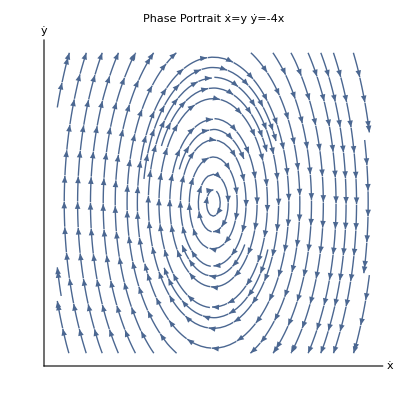

```mathematica
StreamPlot[
{dq4[[1]],dq4[[2]]},{x,-5,5},{y,-5,5},
StreamScale->Automatic,
Axes->True,
Frame->False,
AxesLabel->{"ẋ","ẏ"},
Ticks->None,
PlotLabel->"Phase Portrait\nẋ=y
ẏ=-4x"
]
```

b)   ẋ=2y
ẏ=x

```mathematica
F5={{0,2},{1,0}};
Eigenvalues[F5]
Eigenvectors[F5]
dq5=F5.q;
MatrixForm[%]
```

{-√2,√2}

{{-√2,1},{√2,1}}

(2 y
x)

The eigenvalues associated to the matrix of the system are reals one of them greater than zero and the other one less than zero. Thus, the fixed point x^*=(0,0) is a saddle point and can’t be classified into asymptotically stable, Lyapunov stable or attractor.

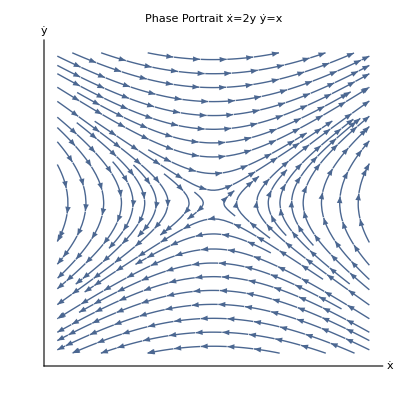

```mathematica
StreamPlot[
{dq5[[1]],dq5[[2]]},{x,-5,5},{y,-5,5},
StreamScale->Automatic,
Axes->True,
Frame->False,
AxesLabel->{"ẋ","ẏ"},
Ticks->None,
PlotLabel->"Phase Portrait\n ẋ=2y
ẏ=x"
]
```

c)   ẋ=0
ẏ=x

```mathematica
F6={{0,0},{1,0}};
Eigenvalues[F6]
Eigenvectors[F6]
dq6=F6.q;
MatrixForm[%]
```

{0,0}

{{0,1},{0,0}}

(0
x)

The eigenvalues associated to the matrix of the system are both zero. In this case, as it can be seen in the phase portrait, the fixed points x^*=(0,y) can’t be classified into asymptotically stable, Lyapunov stable or attractors.

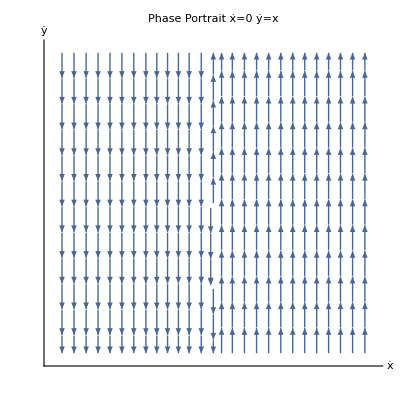

```mathematica
StreamPlot[
{dq6[[1]],dq6[[2]]},{x,-5,5},{y,-5,5},
StreamScale->Automatic,
Axes->True,
Frame->False,
AxesLabel->{"ẋ","ẏ"},
Ticks->None,
PlotLabel->"Phase Portrait\n ẋ=0
ẏ=x"
]
```

d)   ẋ=0
ẏ=-y

```mathematica
F7={{0,0},{0,-1}};
Eigenvalues[F7]
Eigenvectors[F7]
dq7=F7.q;
MatrixForm[%]
```

{-1,0}

{{0,1},{1,0}}

(0
-y)

One of the eigenvalues associated to the matrix of the system is zero, this is a degenerate case. In this one, as it can be seen in the phase portrait, the fixed points x^*=(x,0) are Lyapunov stable.

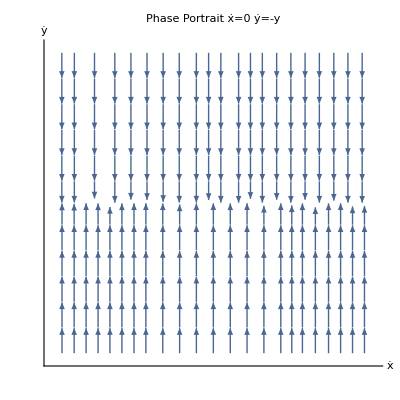

```mathematica
StreamPlot[
{dq7[[1]],dq7[[2]]},{x,-5,5},{y,-5,5},
StreamScale->Automatic,
Axes->True,
Frame->False,
AxesLabel->{"ẋ","ẏ"},
Ticks->None,
PlotLabel->"Phase Portrait\n ẋ=0
ẏ=-y"
]
```

e)   ẋ=-x
ẏ=-5y

```mathematica
F8={{-1,0},{0,-5}};
Eigenvalues[F8]
Eigenvectors[F8]
dq8=F8.q;
MatrixForm[%]
```

{-5,-1}

{{0,1},{1,0}}

(-x
-5 y)

The eigenvalues associated to the matrix of the system are both negative reals. Thus, the fixed point x^*=(0,0) is a node and is asymptotically stable.

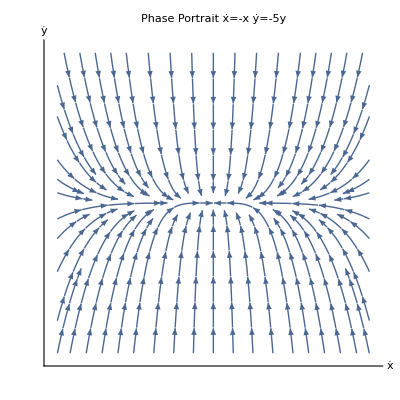

```mathematica
StreamPlot[
{dq8[[1]],dq8[[2]]},{x,-5,5},{y,-5,5},
StreamScale->Automatic,
Axes->True,
Frame->False,
AxesLabel->{"ẋ","ẏ"},
Ticks->None,
PlotLabel->"Phase Portrait\n ẋ=-x
ẏ=-5y"
]
```

f)   ẋ=x
ẏ=y

```mathematica
F9={{1,0},{0,1}};
Eigenvalues[F9]
Eigenvectors[F9]
dq9=F9.q;
MatrixForm[%]
```

{1,1}

{{0,1},{1,0}}

(x
y)

The eigenvalues associated to the matrix of the system are both positive reals. Thus, the fixed point x^*=(0,0) is a node and neither it is attractor nor Lyapunov stable.

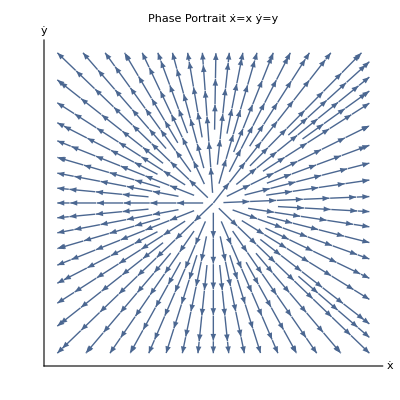

```mathematica
StreamPlot[
{dq9[[1]],dq9[[2]]},{x,-5,5},{y,-5,5},
StreamScale->Automatic,
Axes->True,
Frame->False,
AxesLabel->{"ẋ","ẏ"},
Ticks->None,
PlotLabel->"Phase Portrait\n ẋ=x
ẏ=y"
]
```

## P. IV

5.2.2	 ẋ=x-y
ẏ=x+y.08.08.08

a) The matrix of the system is

```mathematica
F10={{1,-1},{1,1}};
MatrixForm[%]
```

(1 | -1
1 | 1)

The eigenvalues and eigenvectors are:

```mathematica
{λ1,λ2}=Eigenvalues[F10]
{v1,v2}=Eigenvectors[F10]
```

{1+ⅈ,1-ⅈ}

{{ⅈ,1},{-ⅈ,1}}

b)

```mathematica
Simplify[ExpToTrig[C[1] ⅇ^(λ1 t)v1+C[2] ⅇ^(λ2 t)v2]]
```

{ⅈ ((C[1]-C[2]) Cos[t]+ⅈ (C[1]+C[2]) Sin[t]) (Cosh[t]+Sinh[t]),((C[1]+C[2]) Cos[t]+ⅈ (C[1]-C[2]) Sin[t]) (Cosh[t]+Sinh[t])}

So, for the first component of the solution:

ⅈ ( Cos[ t ] ( C[1]-C[2] )+ⅈSin[ t ]( C[1]+C[2] ) )( Cosh[ t ]+Sinh[ t ] )
=ⅇ^t ( -Sin[ t ]( C[1]+C[2] )+ⅈCos[ t ] ( C[1]-C[2] ) )

for the second component:

( Cos[ t ](C[1]+C[2] ) +ⅈSin[ t ]( C[1]-C[2] ) )( Cosh[ t ]+Sinh[ t ] )
=ⅇ^t ( Cos[ t ](C[1]+C[2] ) +ⅈSin[ t ]( C[1]-C[2] ) )

Then, setting A≡C[1]+C[2]  and  B≡C[1]-C[2], the complex solution (x[ t ] ∈ ℂ^2) may be written as:

x[ t ]=A ⅇ^t (-Sin[ t ]
Cos[ t ])+ⅈ B ⅇ^t (Cos[ t ]
Sin[ t ])

The real part and the imaginary part of x[ t ] are both solutions to the system:

```mathematica
TrueQ[D[ⅇ^t ({{-Sin[ t ]}, {Cos[ t ]}}),t]==({{-ⅇ^t Sin[ t ]-ⅇ^t Cos[ t ]}, {-ⅇ^t Sin[ t ]+ⅇ^t Cos[ t ]}})]
TrueQ[D[ⅇ^t ({{Cos[ t ]}, {Sin[ t ]}}),t]== ({{ⅇ^t Cos[ t ]-ⅇ^t Sin[ t ]}, {ⅇ^t Cos[ t ]+ⅇ^t Sin[ t ]}})]
```

True

True

As both are independent solutions, the real solution (x[ t ] ∈ ℝ^2) should be written as

x[ t ]=A ⅇ^t (-Sin[ t ]
Cos[ t ])+ B ⅇ^t (Cos[ t ]
Sin[ t ])

## P. V

5.2.4	   ẋ=5x+10y
ẏ=-x-y.08.08

```mathematica
F11={{5,10},{-1,-1}};
Eigenvalues[F11]
Eigenvectors[F11]
dq11=F11.q;
MatrixForm[%]
```

{2+ⅈ,2-ⅈ}

{{-3-ⅈ,1},{-3+ⅈ,1}}

(5 x+10 y
-x-y)

The eigenvalues associated to the matrix of the system are complex conjugates with positive real part. Thus, the fixed point x^*=(0,0) is an unstable spiral.

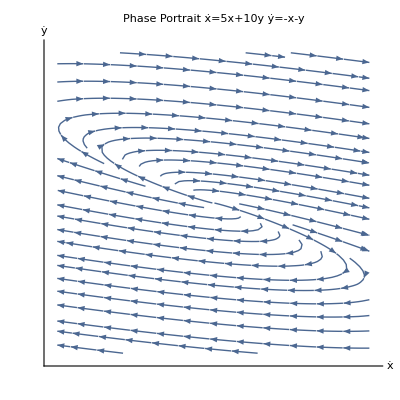

```mathematica
StreamPlot[
{dq11[[1]],dq11[[2]]},{x,-5,5},{y,-5,5},
StreamScale->Automatic,
Axes->True,
Frame->False,
AxesLabel->{"ẋ","ẏ"},
Ticks->None,
PlotLabel->"Phase Portrait\nẋ=5x+10y
ẏ=-x-y"
]
```

5.2.6	   ẋ=-3x+2y
ẏ=x-2y.08.08

```mathematica
F12={{-3,2},{1,-2}};
Eigenvalues[F12]
Eigenvectors[F12]
dq12=F12.q;
MatrixForm[%]
```

{-4,-1}

{{-2,1},{1,1}}

(-3 x+2 y
x-2 y)

The eigenvalues associated to the matrix of the system are positive reals. Thus, the fixed point x^*=(0,0) is an unstable node.

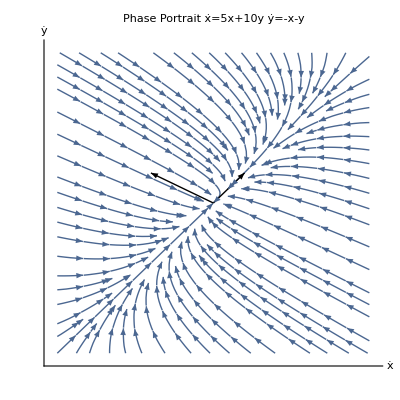

```mathematica
StreamPlot[
{dq12[[1]],dq12[[2]]},{x,-5,5},{y,-5,5},
StreamScale->Automatic,
Axes->True,
Frame->False,
AxesLabel->{"ẋ","ẏ"},
Ticks->None,
PlotLabel->"Phase Portrait\nẋ=5x+10y
ẏ=-x-y",
Epilog->{Arrow[{{0,0},{-2,1}}],Arrow[{{0,0},{1,1}}]}
]
```

The black arrows are the eigenvectors of the matrix.

5.2.8	   ẋ=-3x+4y
ẏ=-2x+3y.08.08

```mathematica
F13={{-3,4},{-2,3}};
Eigenvalues[F13]
Eigenvectors[F13]
dq13=F13.q;
MatrixForm[%]
```

{-1,1}

{{2,1},{1,1}}

(-3 x+4 y
-2 x+3 y)

The eigenvalues associated to the matrix of the system are reals, one positive and one negative. Thus, the fixed point x^*=(0,0) is a saddle node.

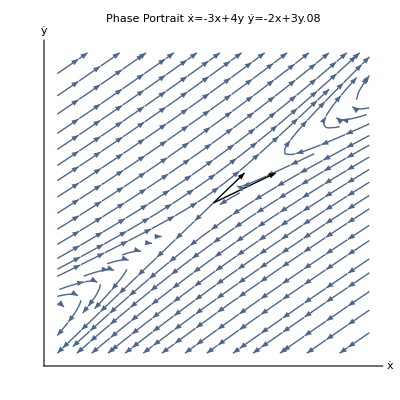

```mathematica
StreamPlot[
{dq13[[1]],dq13[[2]]},{x,-5,5},{y,-5,5},
StreamScale->Automatic,
Axes->True,
Frame->False,
AxesLabel->{"ẋ","ẏ"},
Ticks->None,
PlotLabel->"Phase Portrait\nẋ=-3x+4y
ẏ=-2x+3y.08",
Epilog->{Arrow[{{0,0},{2,1}}],Arrow[{{0,0},{1,1}}]}
]
```

The black arrows are the eigenvectors of the matrix.

## P. VI

5.2.12    L I^(..)+R İ+I/C=0

a) Setting    İ=p   →    ṗ=I^(..)=-R p/L-I/C L   the equivalent linear system is  İ=p
ṗ=-1/(C L)I-R/L p

```mathematica
F14={{0,1},{-1/(Subscript[C, 1] L),-R/L}};
Eigenvalues[F14]
Eigenvectors[F14]
q14={i,p};
dq14=F14.q14;
MatrixForm[%]
```

{(-R C_1-√(-4 L C_1+R^2 C_1^2))/(2 L C_1),(-R C_1+√(-4 L C_1+R^2 C_1^2))/(2 L C_1)}

{{1/2 (-R C_1+√(C_1 (-4 L+R^2 C_1))),1},{1/2 (-R C_1-√(C_1 (-4 L+R^2 C_1))),1}}

(p
-(p R)/L-i/(L C_1))

b) The eigenvalues of the system are λ_1=(-R C_1- √C_1 √(-4 L +R^2 C_1))/(2 L C_1)  &    λ_2=(-R C_1+√C_1 √(-4 L +R^2 C_1))/(2 L C_1) 
If R>0 and:
	· if the eigenvalues are complex with nonvanishing imaginary parts (-4 L +R^2 C_1<0), then the real part of the eigenvalues would be negative (obviously,-C1 R <0). Thus, the 	  fixed point (0,0) would be asymptotically stable (spiral).
	
	· if the eigenvalues are pure reals (-4 L+C_1 R^2 ≥ 0), then λ_1<0 (it follows directly form both conditions). And
	    -R C_1+ √C_1 √(-4 L +R^2 C_1) ≤^?  0       ↔    -4 L C_1 +R^2 C_1^2 ≤^? R^2 C_1^2    ↔   -4 L C_1≤^? 0 
	  As from the hypothesis we have L,C_1>0,  we can drop the question mark (?) and assure that  -4 L C_1≤ 0 and immediately we have -R C_1+ √C_1 √(-4 L +R^2 C_1) ≤  0. That 	  is, the eigenvalue   λ_2<0. And we can affirm that the fixed point (0,0)  –under the mentioned restrictions– would be asymptotically stable (node).

On the other hand, if R=0, we have

```mathematica
Eigenvalues[{{0,1},{-1/(Subscript[C, 1] L),0}}]
```

{-ⅈ/(√L √C_1),ⅈ/(√L √C_1)}

That is, purely imaginary and conjugate eigenvalues. We can say that the fixed point (0,0), in this case, would be neutrally stable (center).





c) From b) we concluded that:
	· If   -4 L +R^2 C_1<0 we get an asymptotically stable spiral or a neutrally stable center –in case R=0.
	· If   -4 L +R^2 C_1>0 we get an asymptotically stable node.

Now we consider the case -4 L +R^2 C_1=0: this assumption would lead to  λ_1=λ_2 and we would get a degenerate case (in this case this condition will lead to degenerate nodes). 

The phase portraits must look something like the next figures:

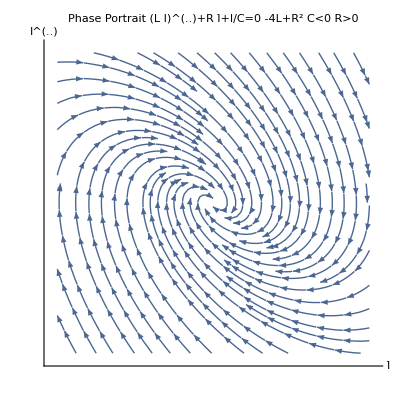

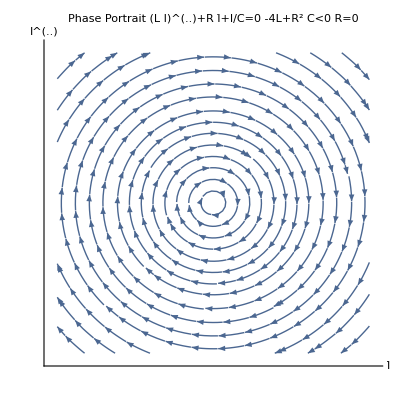

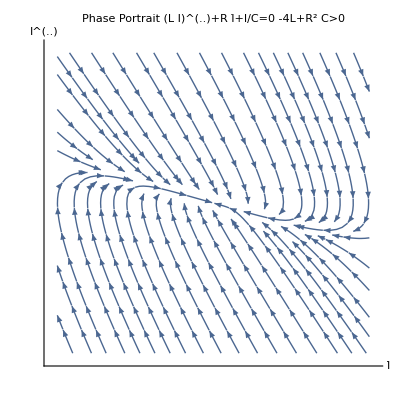

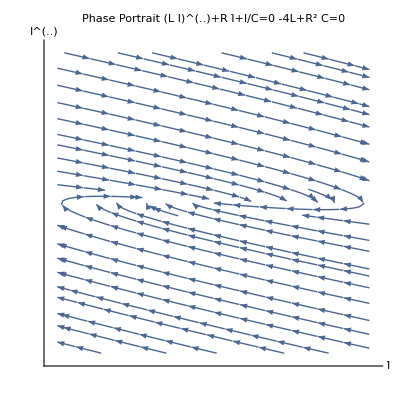

```mathematica
StreamPlot[
{p,-i-p},{i,-5,5},{p,-5,5},
StreamScale->Automatic,
Axes->True,
AxesLabel->{"İ","I^(..)"},
Ticks->None,
Frame->False,

PlotLabel->"Phase Portrait\n(L I)^(..)+R İ+I/C=0    -4L+R^2 C<0      R>0"
]
StreamPlot[
{p,-i},{i,-5,5},{p,-5,5},
StreamScale->Automatic,
Axes->True,
AxesLabel->{"İ","I^(..)"},
Ticks->None,
Frame->False,

PlotLabel->"Phase Portrait\n(L I)^(..)+R İ+I/C=0    -4L+R^2 C<0      R=0"
]
StreamPlot[
{p,-1/2 i-2p},{i,-5,5},{p,-5,5},
StreamScale->Automatic,
Axes->True,
AxesLabel->{"İ","I^(..)"},
Ticks->None,
Frame->False,

PlotLabel->"Phase Portrait\n(L I)^(..)+R İ+I/C=0     -4L+R^2 C>0"
]
StreamPlot[
{p,-1/(4*16)i-1/4 p},{i,-5,5},{p,-5,5},
StreamScale->Automatic,
Axes->True,
AxesLabel->{"İ","I^(..)"},
Ticks->None,
Frame->False,
PlotLabel->"Phase Portrait\n(L I)^(..)+R İ+I/C=0     -4L+R^2 C=0"
]
```